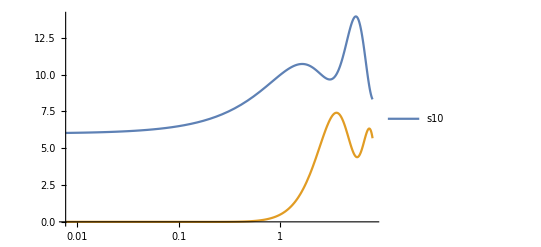

```mathematica
Clear["Global`*"]
k=1;
ti=0;
tf=5*10;
v0=5;
L0=6;
m=1;
f=0.5;
kk=1;
kkk=1;
te=8;
eqns={m a1''[t]==-k (a1[t]-L0-a2[t])-f kkk,m a2''[t]==k (a1[t]-L0-a2[t])-f kk,a1[0]==L0,a1'[0]==v0,a2[0]==0,a2'[0]==0,WhenEvent[Abs[a1'[t]]<=.00001 && Abs[k (a1[t]-L0-a2[t])]<=f +.00001 && Abs[a2'[t]]<=.00001,{te=t,"StopIntegration"}],WhenEvent[ Abs[a2'[t]]>0  Or Abs[k (a1[t]-L0-a2[t])]>f   ,{kk=a2'[t]/(√(a2'[t]^2))}],WhenEvent[a2'[t]==0 && Abs[k (a1[t]-L0-a2[t])]<=f  ,{

kk=(k (a1[t]-L0-a2[t]))/f}],WhenEvent[  Abs[a1'[t]]>0  Or Abs[k (a1[t]-L0-a2[t])]>f  ,{kkk=a1'[t]/(√(a1'[t]^2))}],WhenEvent[a1'[t]==0 && Abs[k (a1[t]-L0-a2[t])]<=f  ,{kkk=-(k (a1[t]-L0-a2[t]))/f}]};
s10=NDSolve[eqns,{a1[t],a2[t]},{t,ti,tf}];

{a1[t_],a2[t_]}={a1[t],a2[t]}/. s10[[1]];

hspring[a0_,x10_,x20_]:=Module[{a=a0,x1=x10,x2=x20,n=60},h=(x2-x1)/n;
xvalues=Table[k,{k,x1,x2,h}];
yvalues=Table[a Sin[m Pi/2],{m,0,n}];
Line[Transpose@{xvalues,yvalues}]];

vspring[a0_,y10_,y20_]:=Module[{a=a0,y1=y10,y2=y20,n=10},h=(y2-y1)/n;
yvalues=Table[k,{k,y1,y2,h}];
xvalues=Table[a Sin[m Pi/2],{m,0,n}];
Line[Transpose@{xvalues,yvalues}]];

Manipulate[
tu1=Plot[{a1[x],a2[x]},{x,ti,t},PlotRange->{{0,te},{0,50}}];
tu2=Graphics[{hspring[0.5,a2[t]+1.2,a1[t]],Black,Line[{{0,-0.6},{15,-0.6}}],Line[{{0,-0.6},{0,1}}],Red,Rectangle[{a1[t],-0.6},{a1[t]+1.2,0.6}],Black,Rectangle[{a2[t],-0.6},{a2[t]+1.2,0.6}]},PlotRange->{{0,100},{-5,5}}];

Grid[{{tu2,tu1}}],
{t,0.01,te},SaveDefinitions->True]

LogLinearPlot[{a1[t],a2[t]},{t,ti,te},PlotRange->Full,PlotLegends->Placed[{"s10"},{.4,.6}]]
```